```mathematica
<<Vilcretas`
```

VilCretas está disponible.

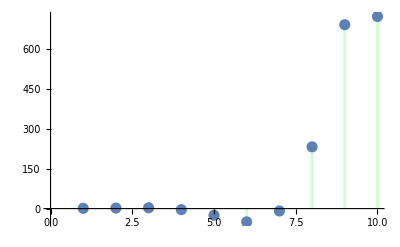

```mathematica
GraficaRRL[{2,-3,-4},{1,2,3}]
```

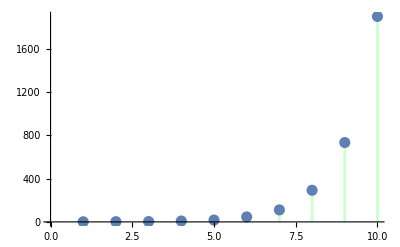

```mathematica
GraficaRRL[{2,3,-4},{1,2,3}]
```

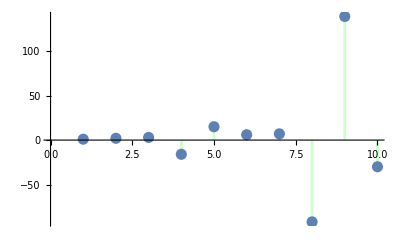

```mathematica
GraficaRRL[{-2,-3,-4},{1,2,3}]
```

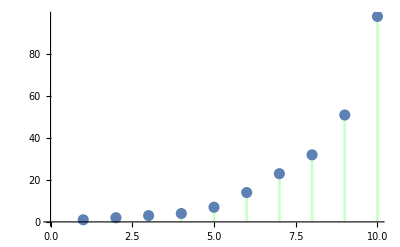

```mathematica
GraficaRRL[{2,-3,4},{1,2,3}]
```

```mathematica
?GraficaRRL
```

```mathematica
Last[RT[{-2,0,5,-9},{-2,-9,0},49, inicio->2]]
```

-300933275756066

```mathematica
(-22*6^5-2*6^2)/(-20*6^5-7*6^2+9)
```

19016/17307

```mathematica
FindRRHL[{-5,-3,-7,-43,5,-439,665,-5251,13853,-70975},a,n]
```

{a[n]==6 a[-3+n]+9 a[-2+n]-2 a[-1+n],a[1]==-5,a[2]==-3,a[3]==-7,(Root2.52Root[-6-9 #1+2 #1^2+#1^3&,3]2.518816693272298)^n Root-0.641Root[-989-14192 #1-17616 #1^2+3303 #1^3&,1]-0.6410052635143305+(Root-3.91Root[-6-9 #1+2 #1^2+#1^3&,1]-3.9095159661559507)^n Root-0.0772Root[-989-14192 #1-17616 #1^2+3303 #1^3&,2]-0.07718999848869701+(Root-0.609Root[-6-9 #1+2 #1^2+#1^3&,2]-0.609300727116347)^n Root6.05Root[-989-14192 #1-17616 #1^2+3303 #1^3&,3]6.051528595336361}

```mathematica
MetodoRRHL[{4,-4},{9,1},n,b]
```

La ecuación característica corresponde a: 4-4 n+n^2=0

Raíz o raíces de la ecuación característica: {2,2}

La forma que toma la solución de la relación de recurrencia es: 2^n b_1+2^n n b_2

El sistema de ecuaciones a resolver corresponde a: {2 (b_1+b_2)==9,4 (b_1+2 b_2)==1}

La solución del sistema de ecuaciones es: {b_1→35/4,b_2→-17/4}

La solución de la relación de recurrencia corresponde a: -2^(-2+n) (-35+17 n)

```mathematica
MetodoRRHL[{4,-4},{3,1},n,b]
```

La ecuación característica corresponde a: 4-4 n+n^2=0

Raíz o raíces de la ecuación característica: {2,2}

La forma que toma la solución de la relación de recurrencia es: 2^n b_1+2^n n b_2

El sistema de ecuaciones a resolver corresponde a: {2 (b_1+b_2)==3,4 (b_1+2 b_2)==1}

La solución del sistema de ecuaciones es: {b_1→11/4,b_2→-5/4}

La solución de la relación de recurrencia corresponde a: -2^(-2+n) (-11+5 n)

```mathematica
Table[2/5(-1/7)^n-3/4(1/5)^n,{n,5,30}];
```

```mathematica
FindRRHL[Table[2/5(-1/7)^n-3/4(1/5)^n,{n,5,15}],a,n]
```

{a[n]==1/35 a[-2+n]+2/35 a[-1+n],a[1]==-55421/210087500,a[2]==-327947/7353062500,1/4 35^(-4-n) (8 (-1)^n 5^(3+n)-3 7^(4+n))}

```mathematica
programa[n_]:=Module[{paux}, 
paux[m_, Cont_:1,p_]:=If[m==1,7,
If[m==Cont, p,paux[m, Cont+1, p * 7]]];
paux[n,7]]
```

for(int i = 0; i < m; i++){
	p *= 7;
}

```mathematica
7^2
```

49

```mathematica
Sort[Solve[t^4-1 t^3-3 t^2+36+108t==0]]
```

{{t→Root-4.53Root[36+108 #1-3 #1^2-#1^3+#1^4&,1]-4.5324641891351405},{t→Root-0.331Root[36+108 #1-3 #1^2-#1^3+#1^4&,2]-0.33074053327327296},{t→Root2.93-3.93 ⅈRoot[36+108 #1-3 #1^2-#1^3+#1^4&,3]2.9316023612042064},{t→Root2.93+3.93 ⅈRoot[36+108 #1-3 #1^2-#1^3+#1^4&,4]2.9316023612042064}}

```mathematica
MetodoRRHL[{-3,36,108},{1,1,2},n,b]
```

La ecuación característica corresponde a: -108-36 n+3 n^2+n^3=0

Raíz o raíces de la ecuación característica: {-6,-3,6}

La forma que toma la solución de la relación de recurrencia es: (-6)^n b_1+(-3)^n b_2+6^n b_3

El sistema de ecuaciones a resolver corresponde a: {-3 (2 b_1+b_2-2 b_3)==1,9 (4 b_1+b_2+4 b_3)==1,-27 (8 b_1+b_2-8 b_3)==2}

La solución del sistema de ecuaciones es: {b_1→19/216,b_2→-34/81,b_3→29/648}

La solución de la relación de recurrencia corresponde a: 1/8 3^(-4+n) (57 (-2)^n-272 (-1)^n+29 2^n)

-a[n] = -108a[n-3]-36a[n-2]+3a[n-1]
a[n] = 108a[n-3]+36a[n-2]-3a[n-1]

```mathematica
Sort[Solve[t^3+3 t^2-36t-108==0]]
```

{{t→-6},{t→-3},{t→6}}